```mathematica
f = (1-(s-1)^2)^(1/2);
h =  -2 (1-0.5 s)^(1/2);
g = (f-h)/2 Cos[200 s] + (f+h)/2
```

1/2 (√(1-(-1+s)^2)-2 √(1-0.5 s))+1/2 (√(1-(-1+s)^2)+2 √(1-0.5 s)) Cos[200 s]

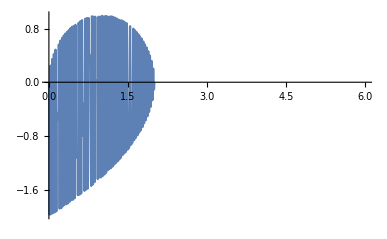

```mathematica
Plot[g, {s,0,6}]
```

```mathematica
absG= Abs[g]
```

Abs[1/2 (√(1-(-1+s)^2)-2 √(1-0.5 s))+1/2 (√(1-(-1+s)^2)+2 √(1-0.5 s)) Cos[200 s]]

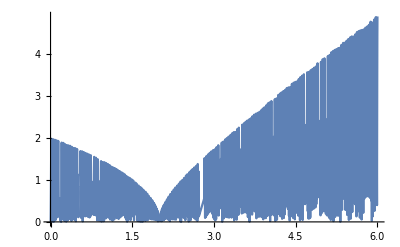

```mathematica
Plot[absG,{s,0,6}]
```